```mathematica
(* IMPORT MODULES *)
ClearAll[m1,m2,m3]
loadDumpSaves=True;
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/hamiltonian.nb"];
NotebookEvaluate["modules/parameters.nb"];
NotebookEvaluate["modules/golden_search.nb"];
If[loadDumpSaves,NotebookEvaluate["modules/load_dump_saves.nb"]];
SetDirectory[NotebookDirectory[]];
```

```mathematica
wMin
```

0.0185221

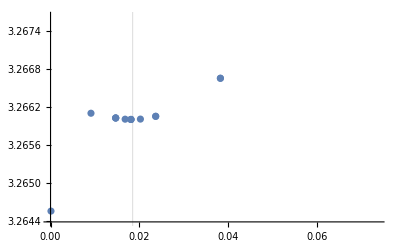

```mathematica
ListPlot[data,GridLines->{{wMin},None}]
```

```mathematica
ClearAll[J,P,FlavourSym,γMax,Λ,m1,m2,m3,ham,sM,t1,t2];
(**** !!!TUNABLE PARAMETERS!!! ****)
J=1/2;(* Total angular momentum J = Λ + S *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
FlavourSym=1;(* Flavour symmetry 1 = symmetric, 0 = antisymmetric *)
γMax=6;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
S=1/2;(* Total spin *)
m1=cq;(* mass of quark 1 *)
m2=cq;(* mass of quark 2 *)
m3=uq;(* mass of quark 3 *)
excited=0;(* Choose excited state, 0 for ground state *)
temperature=0.47;
(**** !!!END OF TUNABLE PARAMETERS!!! ****)
(* Choose to project depending if m1=m2 or m1≠m2, True and False, respectively *)

(* all different masses = 0, two equal masses = 1, all equal masses = 2 *)
case=If[m1==m2,1,0];
case=If[m1==m2==m3,2,case];
states=allStates[J,P,Λ,S,γMax];
sM=stateMatrix[J,P,Λ,S,γMax];

(* Calculate generalised transformation matrices *)
{t1time,t1}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,1]];
Print["Time taken to compute t1: ", ToString[t1time]];
{t2time,t2}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,2]];
Print["Time taken to compute t2: ", ToString[t2time]];

(* Obtain projector matrix *)
proj=projector[states,FlavourSym,case];

(* Required matrices for hamiltonian *)
vCoulomb=polynomialOperatorRho[sM,-1];(* 1/ρ matrix dimensionless *)
vLinear=polynomialOperatorRho[sM,1];(* ρ matrix dimensionless *)
qhoSpect=qhoSpectrum[sM];
kineticRho=polynomialOperatorRho[sM,2];
kineticLam=polynomialOperatorLambda[sM,2];

(* Define Hamiltonian function to be optimised *)
ham[ω_]:=Hb2[ω,temperature,m1,m2,m3,proj];

If[loadDumpSaves,
DumpSave["modules/dumpSave/summationVariables.mx",summationVariables];
DumpSave["modules/dumpSave/talmi.mx",talmi]];
```

Time taken to compute t1: 0.022411

Time taken to compute t2: 0.01987

```mathematica
ClearAll[minTime,a,b,wMin,eigvalMin,evec,rhoSqrd12,rhoSqrd23,rhoSqrd31,rhos,expValsRho,lamSqrd12,lamSqrd23,lamSqrd31,lams,expValsLam,hamiltonian]
(* Golden search parameters *)
wLeft=0.0001;(* min of search range *)
wRight=0.1;(* max of search range *)
tolerance=0.005;(* tolerance of golden search *)

(* Perform golden search *)
{minTime,{a,b,data}}=AbsoluteTiming[goldenSearch[ham,excited+1,wLeft,wRight,tolerance]];
Print["Time taken to find minimum: ", ToString[minTime]];
wMin=(a+b)/2;

(* Obtain Hamiltonian and eigenvalue using optimum ω *)
hamiltonian=ham[wMin];
eigvalMin=Eigenvalues[hamiltonian][[-excited-1]];
Print["{ω_min, E_min}: ",{Around[wMin,a-wMin],eigvalMin}];
Print["Number of basis functions (matrix size): ", Length[hamiltonian]]
```

Time taken to find minimum: 52.4425

{ω_min, E_min}: {0.01850.0017,3.266}

Number of basis functions (matrix size): 20

```mathematica
(* Obtain eigenvector of total hamiltonian *)
evec=Eigenvectors[hamiltonian][[-1]];

(* Find expectation values of <ρ^2> *)
rhoSqrd12=1/α[m1,m2,wMin]^2 kineticRho;
rhoSqrd23=1/α1[m1,m2,m3,wMin]^2 Transpose[t1].kineticRho.t1;
rhoSqrd31=1/α2[m1,m2,m3,wMin]^2 Transpose[t2].kineticRho.t2;

rhos={rhoSqrd12,rhoSqrd23,rhoSqrd31};
expValsRho=Table[√(evec.(Transpose[proj].rhos[[i]].proj).evec)/5.068,{i,1,3}]
Print["Expectation Values of √(<SuperscriptBox[SubscriptBox[ρ, i], 2]>) for pairs {12, 23, 31} in (fm): ",expValsRho]
Print["Expectation Values as ratios: ",expValsRho/Max[expValsRho]]

(* Find expectation values of <λ^2> *)
lamSqrd12=1/β[m1,m2,m3,wMin]^2 kineticLam;
lamSqrd23=1/β1[m1,m2,m3,wMin]^2 Transpose[t1].kineticLam.t1;
lamSqrd31=1/β2[m1,m2,m3,wMin]^2 Transpose[t2].kineticLam.t2;
lams={lamSqrd12,lamSqrd23,lamSqrd31};
expValsLam=Table[evec.(Transpose[proj].lams[[i]].proj).evec,{i,1,3}];
```

{1.93116,5.07577,5.07577}

Expectation Values of √(<SuperscriptBox[SubscriptBox[ρ, i], 2]>) for pairs {12, 23, 31} in (fm): {1.93116,5.07577,5.07577}

Expectation Values as ratios: {0.380465,1.,1.}

```mathematica
(* Mean mass-square radius using exact method *)
expVals=expValsLam/5.068^2;
λ3Squared=expVals[[1]];
λ1Squared=expVals[[2]];
λ2Squared=expVals[[3]];
M=m1+m2+m3;
term1=(m1(m2+m3)^2)/M^3 λ1Squared;
term2=(m2(m1+m3)^2)/M^3 λ2Squared;
term3=(m3(m1+m2)^2)/M^3 λ3Squared;
RmSquared=term1+term2+term3;
InputForm[Round[{temperature,RmSquared},10^-5]*1.]
```

{0.47, 3.01795}

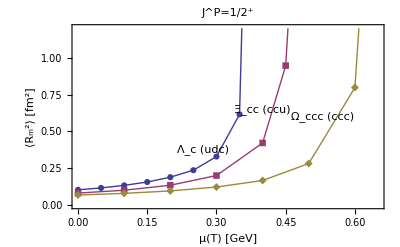

```mathematica
RmSudc={{0.0001,0.1039},{0.05,0.11702},{0.1,0.13433},{0.15,0.15699},{0.2,0.18978},{0.25,0.23731},{0.3,0.32973}(*,{0.325,0.42641}*),{0.35,0.61606},{0.4,6.47471}};
RmSccu={{0.0001,0.08211},{0.1,0.10139},{0.2,0.13528},{0.3,0.20094},{0.4,0.42198},{0.45,0.94642},{0.5,3.52382}};
RmSccc={{0.00001,0.06889},{0.1,0.08001},{0.2,0.09661},{0.3,0.12301},{0.4,0.16757},{0.5,0.28264},{0.6,0.79778},{0.65,3.15219}};
plot=ListPlot[{RmSudc,RmSccu,RmSccc},
Joined->True,
PlotMarkers->Automatic,
(*GridLines->{{0.36,0.46,0.615},None},*)
Frame->True,
FrameLabel->{"μ(T) [GeV]","⟨R_m^2⟩ [fm^2]"},
LabelStyle->{FontFamily->"Times",FontSize->14},
PlotRange->{{0,0.65},{0,1.2}},
PlotTheme->"Classic",
PlotLabel->"J^P=1/2^+"
];
text1=Graphics[{Text[Style["Λ_c (udc)",Medium,FontFamily->"Times"],{0.27,0.38},{0,0},{3,2.5}]}];
text2=Graphics[{Text[Style["Ξ_cc (ccu)",Medium,FontFamily->"Times"],{0.4,0.65},{0,0},{2.3,7.6}]}];
text3=Graphics[{Text[Style["Ω_ccc (ccc)",Medium,FontFamily->"Times"],{0.53,0.6},{0,0},{2,3.5}]}];
combinedPlot=Show[plot,text1,text2,text3]
```

```mathematica
Export["plots/ch7_v2_RmS_charmed.pdf",combinedPlot,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

plots/ch7_v2_RmS_charmed.pdf

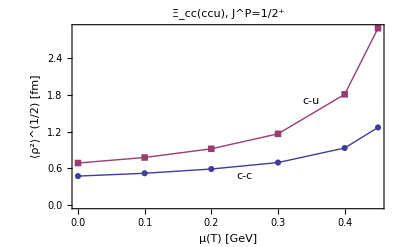

```mathematica
ccuRcc={{0,0.47431294305067734},{0.1,0.5203017694963563},{0.2,0.589767288508385},{0.3,0.6949624925555078},{0.4,0.9322494165414886},{0.45,1.267443827663006}};
ccuRcu={{0,0.6875801386811375},{0.1,0.7774354480131888},{0.2,0.9195211284798689},{0.3,1.1635998281154005},{0.4,1.8073528060188082},{0.45,2.885303869232576}};
plot=ListPlot[{ccuRcc,ccuRcu},
Joined->True,
PlotMarkers->Automatic,
Frame->True,
FrameLabel->{"μ(T) [GeV]","⟨ρ^2⟩^(1/2) [fm]"},
LabelStyle->{FontFamily->"Times",FontSize->14},
PlotLabel->"Ξ_cc(ccu), J^P=1/2^+",
PlotTheme->"Classic"
];
text1=Graphics[{Text[Style["c-c",Medium,FontFamily->"Times"],{0.25,0.48},{0,0},{1,0.1}]}];
text2=Graphics[{Text[Style["c-u",Medium,FontFamily->"Times"],{0.35,1.7},{0,0},{1,0.6}]}];
combined=Show[plot,text1,text2]
```

```mathematica
Export["plots/ch7_v2_ccu_cc_vs_cu.pdf",combined,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

plots/ch7_v2_ccu_cc_vs_cu.pdf

```mathematica
(* ccu temperature triangles *)
baryon="ccu";
temps={0,0.1,0.2,0.3,0.4,0.45};
lengths={
{0.47431294305067734,0.6875801386811375,0.6875801386811388},(* μ=0.0001 *)
{0.5203017694963563,0.7774354480131888,0.7774354480131903},(* μ=0.1 *)
{0.589767288508385,0.9195211284798689,0.9195211284798704},(* μ=0.2 *)
{0.6949624925555078,1.1635998281154005,1.1635998281154023},(* μ=0.3 *)
{0.9322494165414886,1.8073528060188082,1.8073528060188113},(* μ=0.4 *)
{1.267443827663006,2.885303869232576,2.8853038692325805}(* μ=0.45 *)
};

excitedTriangle[i_]:=Module[{},
{q1,q2,q3}=StringTake[baryon,{{1},{2},{3}}];
{p12,p23,p31}=lengths[[i]];
t=SSSTriangle[p23,p12,p31];
{cx,cy}=RegionCentroid[t];

AppendTo[t[[1]],{0.00000001,0.00000001}];

SetOptions[ListLinePlot,
PlotStyle->{Gray,Dashed},
BaseStyle->{FontFamily->"Times",FontSize->12},
AspectRatio->Automatic];

ListLinePlot[t[[1]]->{q1,q3,q2,None},
Axes->{None,None},
Frame->{{None,True},{True,None}},
FrameStyle->Directive[Opacity[0.7],Gray,Dashed],
FrameTicks->{{0,1,2,3},{0,1,2}},
PlotRange->{{-0.6,3.5},{-0.5,2.2}},
LabelingFunction->Automatic,
PlotMarkers->{●, 8},
text=Style[("μ(T)="<>ToString[temps[[i]]]<>" GeV"),Medium];
PlotLegends->{Placed[text,{0.4,0.9}]},
LabelStyle->{FontFamily->"Times",FontSize->12}
]
]
color=Gray//Lighter;
t=Grid[
Table[excitedTriangle[3i+j+1],{i,0,1},{j,0,2}],
ItemSize->All,
Dividers->{{2->{White},3->{White}},{2->{White}}}
]
```

-Graphics-

```mathematica
Export["plots/ch7_v2_ccu_triangles.pdf",t]
```

plots/ch7_v2_ccu_triangles.pdf

```mathematica
(* uuc temperature triangles *)
baryon="uuc";
lengths={
{0.7696265593152541,0.703862778144469,0.7038627781444696},
{0.8789990662411297,0.7999710127504313,0.7999710127504319},
{1.0540858542987452,0.949955141435567,0.9499551414355677},
{1.416229327056464,1.2495927675977625,1.2495927675977634},
{1.7630436052259275,1.5279743865359061,1.5279743865359074},
{1.9840168132360794,1.7032926818089578,1.703292681808959}
};
excitedTriangle[i_]:=Module[{},
{q1,q2,q3}=StringTake[baryon,{{1},{2},{3}}];
{p12,p23,p31}=lengths[[i]];
t=SSSTriangle[p23,p12,p31];
{cx,cy}=RegionCentroid[t];

AppendTo[t[[1]],{0.000001,0.0000001}];

SetOptions[ListLinePlot,PlotStyle->{Gray,Dashed},BaseStyle->{FontFamily->"Times",FontSize->12},AspectRatio->Automatic];

ListLinePlot[t[[1]]->{q1,q3,q2,None},
Axes->None,
(*PlotRange->{{-0.3,1.5},{-0.1,1.0}},*)
PlotRange->{{-0.6,2.5},{-0.5,2.0}},
LabelingFunction->Automatic,
PlotMarkers->{●, 8},
PlotLegends->{Placed["n="<>ToString[i-1],{0,0.9}]},
LabelStyle->{FontFamily->"Times"}]
]
color=Gray//Lighter;
t=Grid[Table[excitedTriangle[3i+j+1],{i,0,1},{j,0,2}],ItemSize->All,Dividers->{{2->{color},3->{color}},{2->{color}}}]
```

-Graphics-

```mathematica
Export["plots/Silvestre/triangles/ubbExcited.pdf",t]
```

plots/Silvestre/triangles/ubbExcited.pdf

```mathematica
(* Random, unexcited states *)
baryons={
{"udc",{0.770,0.707,0.707}},
{"uuc",{0.924,0.751,0.751}},
{"udb",{0.764,0.675,0.675}},
{"uub",{0.930,0.739,0.739}},
{"ubb",{0.657,0.296,0.657}},
{"ccb",{0.426,0.368,0.368}}
};
fontColour=Gray//Darker;
names={
Style["Λ_c",Bold,fontColour],
Style["Σ_c",Bold,fontColour],
Style["Λ_b",Bold,fontColour],
Style["Σ_b",Bold,fontColour],
Style["Ξ_bb",Bold,fontColour],
Style["Ω_ccb",Bold,fontColour]
};
triangle[i_]:=Module[{quarks,t,cx,cy},
quarks=baryons[[i,1]];
{p12,p23,p31}=baryons[[i,2]];
{q1,q2,q3}=StringTake[quarks,{{1},{2},{3}}];
t=SSSTriangle[p23/0.924,p12/0.924,p31/0.924];
{cx,cy}=RegionCentroid[t];

AppendTo[t[[1]],{0.000001,0.0000001}];

SetOptions[ListLinePlot,PlotStyle->{Gray,Dashed},BaseStyle->{FontFamily->"Times",FontSize->12},AspectRatio->Automatic];

ListLinePlot[t[[1]]->{q1,q3,q2,None},Axes->None,PlotRange->{{-0.2,1},{-0.05,0.9}},LabelingFunction->Automatic,PlotMarkers->{●, 8},PlotLegends->Placed[names[[i]],{0.1,0.9}]]
]
color=Gray//Lighter;
t=Grid[Table[triangle[3i+j+1],{i,0,1},{j,0,2}],ItemSize->All,Dividers->{{2->{color},3->{color}},{2->{color}}}]
Export["plots/Silvestre/triangles/randomUnexcited.pdf",t]
```

-Graphics-

plots/Silvestre/triangles/randomUnexcited.pdf